# Input

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
brzgamma=1.533*10^-3;
```

## MuC @ 3 TeV

```mathematica
higgsobsMuC310p[kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_]:={kw^2 kb^2/ktotal,kw^2 kc^2/ktotal,kw^2 kg^2/ktotal,kw^2 ktau^2/ktotal,kw^2 kw^2/ktotal,kw^2 kw^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kgamma^2/ktotal(*,kw^2 kzgamma^2/ktotal*),kw^2 kmu^2/ktotal,kz^2 kb^2/ktotal,kz^2 kc^2/ktotal,kz^2 kg^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kw^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kt^2 kb^2/ktotal(*adding ttH *),kz^2,kz^2brinv+1};
(*adding ttH so that the fit closed*)
higgspreMuC3={0.8,12,2.8,3.8,1.6,5.4,48,12,65,6.4(*,45*),28,2.6,72,14,21,8.4,17,34,23,61(*adding ttH *),3.94,0.05}/100;
inputcorrelationsMuC3=(*06/14/2023*)IdentityMatrix[22]*100(*+halfcorrelationᵀ+halfcorrelation*);
inverseinputcorrelationsMuC3=Inverse[inputcorrelationsMuC3/100];
chisquarehtt3[kw_,kz_,kt_]:=2.2*10^2(kw*kt-1)^2+2.9*(kz*kt-1)^2-23*(kw*kt-1)(kz*kt-1)-1.2*10^3(kw*kt-1)^3+10*(kz*kt-1)^3+92*(kw*kt-1)^2(kz*kt-1)-1.3*10^2(kw*kt-1)(kz*kt-1)^2+3.1*10^3*(kw*kt-1)^4+38*(kz*kt-1)^4+6.9*10^2(kw*kt-1)^2(kz*kt-1)^2;
chisquareMuC310p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]
```

## MuC @ 10 TeV

```mathematica
higgsobsMuC1010p[kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_]:={kw^2 kb^2/ktotal,kw^2 kc^2/ktotal,kw^2 kg^2/ktotal,kw^2 ktau^2/ktotal,kw^2 kw^2/ktotal,kw^2 kw^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kz^2/ktotal,kw^2 kgamma^2/ktotal(*,kw^2 kzgamma^2/ktotal*),kw^2 kmu^2/ktotal,kz^2 kb^2/ktotal,kz^2 kc^2/ktotal,kz^2 kg^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kw^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2,kz^2brinv+1};
higgspreMuC10={0.22,3.6,0.79,1.1,0.42,1.2,13,3.4,15,1.7(*,12*),5.7,0.77,17,3.3,4.8,2.0,4.4,11,4.8,0.75,0.05}/100;
inputcorrelationsMuC10=(*06/14/2023*)IdentityMatrix[21]*100(*+halfcorrelationᵀ+halfcorrelation*);
inverseinputcorrelationsMuC10=Inverse[inputcorrelationsMuC10/100];
chisquarehtt10[kw_,kz_,kt_]:=6.2*10^3(kw*kt-1)^2+1*10^2*(kz*kt-1)^2-6.6*10^2(kw*kt-1)(kz*kt-1)-4.7*10^4(kw*kt-1)^3+4.4*10^2(kz*kt-1)^3+4.0*10^3(kw*kt-1)^2(kz*kt-1)-5.1*10^3(kw*kt-1)(kz*kt-1)^2+2.1*10^5*(kw*kt-1)^4+2.6*10^3(kz*kt-1)^4+4.7*10^4(kw*kt-1)^2(kz*kt-1)^2;
chisquareMuC1010p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]
```

## MuC @ 125 GeV

```mathematica
higgsobsMuC12510p[kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_]:={kmu^2 kmu^2/ktotal,kmu^2 ktau^2/ktotal,kmu^2 kgamma^2/ktotal,kmu^2 kw^2/ktotal,kmu^2 kz^2/ktotal,kmu^2 kg^2/ktotal,kmu^2 kt^2/ktotal,kmu^2 kb^2/ktotal,ktotal,ktotal};
higgspreMuC125={Infinity,2.4,94,0.84,2.9,5.3,12,1.03,3.22,2.80}/100;
halfcorrelationMuC125=SparseArray[{{4,10}->0.625,{8,9}->0.762,{10,10}->0}]//Normal;
inputcorrelationsMuC125 = IdentityMatrix[10]*100+halfcorrelationMuC125ᵀ+halfcorrelationMuC125;
inverseinputcorrelationsMuC125=Inverse[inputcorrelationsMuC125/100];
chisquareMuC12510p[{kz_,kw_,kg_,kgamma_,kb_,kt_,kc_,ktau_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]
```

## HL-LHC

```mathematica
higgsobsLHC10p[kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kgamma^2/ktotal,kg^2 kz^2/ktotal,kg^2 kw^2/ktotal,kg^2 ktau^2/ktotal,kg^2 kb^2/ktotal,kg^2 kmu^2/ktotal,8/11 kw^2 kgamma^2/ktotal+3/11 kz^2 kgamma^2/ktotal,8/11 kw^2 kz^2/ktotal+3/11 kz^2 kz^2/ktotal,8/11 kw^2 kw^2/ktotal+3/11 kz^2 kw^2/ktotal,8/11 kw^2 ktau^2/ktotal+3/11 kz^2 ktau^2/ktotal,8/11 kw^2 kmu^2/ktotal+3/11 kz^2 kmu^2/ktotal,8/11 kw^2 kz^2/ktotal+3/11 kz^2 kz^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kz^2/ktotal,kw^2 kw^2/ktotal,kw^2 kb^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^2 kb^2/ktotal,kt^2 kgamma^2/ktotal,kt^2 kz^2/ktotal,kt^2 kw^2/ktotal,kt^2 kb^2/ktotal,kt^2 ktau^2/ktotal,3/11kz^2brinv+8/11kw^2brinv+1};
higgspreLHC={4.2,4.0,3.7,5.5,24.7,13.8,12.8,13.4,7.3,4.4,54.0,13.9,47.8,13.8,9.4,23.3,78.6,18.4,6.5,9.4,24.6,9.7,11.6,14.9,2.2}/100;
halfcorrelationLHC=({{0, 48, 54, 46, -1, 14, -18, 2, -1, 2, 1, 0, 1, 2, 0, -3, 3, 6, 2, 8, 0, 2, 0, 1, 0}, {0, 0, 52, 37, -1, 13, 0, -11, -3, 0, -1, 1, 1, 1, -1, 1, -9, 6, 2, 1, 5, 1, 0, 1, 0}, {0, 0, 0, 42, -1, 15, -1, -2, -9, -1, -1, 1, 0, 0, 0, 0, -1, 10, 2, 1, 0, 2, 0, 1, 0}, {0, 0, 0, 0, -1, 11, 12, 5, 2, -16, 2, 5, 1, 2, 0, 5, 5, 5, 2, 3, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, -2, 0, 0, 0, -1, -1, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 0, -53, 1, 0, 0, 0, 0, 1, 2, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 5, 6, 8, 1, 3, 0, 1, 0, 2, 2, 1, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 7, 7, 3, 2, 0, 1, 0, 2, 6, 0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 10, 1, 2, 0, 5, 0, 1, 0, 4, 0, 1, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2, 4, 1, 3, 0, 2, 1, 1, 0, 2, 1, 2, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -33, 1, 0, 0, -5, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -68, 0, 0, 0, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -1, 0, 1, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, -1, -6, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 1, -10, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -8, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 8, 18, 16, 11, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 5, 2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 14, -7, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 9, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});(*07/27/2023*)
inputcorrelationsLHC = (*07/27/2023*)IdentityMatrix[25]*100+halfcorrelationLHCᵀ+halfcorrelationLHC;
inverseinputcorrelationsLHC=Inverse[inputcorrelationsLHC/100];
chisquareLHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
```

## CEPC @ 240 GeV

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,(*kt_,*)kc_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kc^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
higgsprecepc=(*Apr.04.2022; Note that the second to last entry is infinity to avoid double counting*){6.36,0.42,3.02,0.53,4.17,0.81,2.02,0.14,1.59,(*Infinity*)(0.00401209+0.00402172)*100/2,0.26,0.07}/100;
(*higgsobscepcinv=0.07/100;*)
halfcorrelationcepc=(*Apr.15.2018*)SparseArray[{{12,12}->0,{4,2}->-13.286,{5,2}->-6.669,{6,2}->0.864,{7,2}->0.638,{8,2}->-0.025,{9,2}->-0.011,{10,2}->-0.075,{5,4}->-32.350,{6,4}->-3.644,{7,4}->-2.869,{8,4}->1.140,{9,4}->-0.521,{10,4}->0.328,{6,5}->-1.926,{7,5}->-1.167,{8,5}->-1.809,{9,5}->0.827,{10,5}->0.148,{7,6}->-22.332,{8,6}->-12.429,{9,6}-> 5.681,{10,6}->-1.680,{8,7}-> -7.027,{9,7}-> 3.212,{10,7}-> -6.498,{9,8}-> -45.706,{10,8}-> 0.918,{10,9}-> -0.420}]//Normal;
inputcorrelationscepc=(*Apr.15.2018*)IdentityMatrix[12]*100+halfcorrelationcepcᵀ+halfcorrelationcepc;
inverseinputcorrelationscepc=Inverse[inputcorrelationscepc/100];
chisquarecepc10p[{kb_,(*kt_,*)kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
```

## CEPC @ 240GeV+360 GeV

```mathematica
higgsobscepc36010p[kz_,kw_,kg_,kgamma_,kb_,(*kt_,*)kc_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kc^2/ktotal,kz^2 kb^2/ktotal,kz^2,kw^2 kmu^2/ktotal,kw^2 ktau^2/ktotal,kw^2 kgamma^2/ktotal,kw^2 kw^2/ktotal,kw^2 kz^2/ktotal,kw^2 kg^2/ktotal,kw^2 kc^2/ktotal,kw^2 kb^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kg^2/ktotal,kz^2 kc^2/ktotal,kz^2 kb^2/ktotal};
higgsprecepc360={41,2.1,11,2.80,20,3.40,8.80,0.90,1.40,57,4.2,16,4.4,21,4.5,16,1.10,6.5,7.5,12,20,4.3}/100;
inputcorrelationscepc360=IdentityMatrix[22]*100;
inverseinputcorrelationscepc360=Inverse[inputcorrelationscepc360/100];
chisquarecepc36010p[{kb_,(*kt_,*)kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]
```

## Combined Chi square

```mathematica
chisquareMuC3LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC10LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]

chisquarecepcLHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquarecepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]

chisquareMuC10cepcLHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]

chisquareMuC10cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC3cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]


chisquareMuC3MuC125cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC10MuC125cepc360LHC10p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelationscepc[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc360[[i]])((higgsobscepc36010p[kz,kw,kg,kgamma,kb,(*kt,*)kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc360[[j]])inverseinputcorrelationscepc360[[i,j]]/lumif,{i,1,Length[higgsprecepc360]},{j,1,Length[higgsprecepc360]}]+Sum[((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreLHC[[i]])((higgsobsLHC10p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreLHC[[j]])inverseinputcorrelationsLHC[[i,j]]/lumif,{i,1,Length[higgspreLHC]},{j,1,Length[higgspreLHC]}]
chisquareMuC3MuC12510p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC3[[i]])((higgsobsMuC310p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC3[[j]])inverseinputcorrelationsMuC3[[i,j]]/lumif,{i,1,Length[higgspreMuC3]},{j,1,Length[higgspreMuC3]}]+chisquarehtt3[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]
chisquareMuC10MuC12510p[{kb_,kt_,kc_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[i]]-1)/higgspreMuC10[[i]])((higgsobsMuC1010p[kz,kw,kg,kgamma,kb,kt,kc,ktau, kmu, brinv, ktotal][[j]]-1)/higgspreMuC10[[j]])inverseinputcorrelationsMuC10[[i,j]]/lumif,{i,1,Length[higgspreMuC10]},{j,1,Length[higgspreMuC10]}]+chisquarehtt10[kw,kz,kt]+Sum[((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)/higgspreMuC125[[i]])((higgsobsMuC12510p[kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[j]]-1)/higgspreMuC125[[j]])inverseinputcorrelationsMuC125[[i,j]]/lumif,{i,1,Length[higgspreMuC125]},{j,1,Length[higgspreMuC125]}]
```

# Fit

### 10p fit only MuC 10TeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC1010p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC1010p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0,kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>=(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC1010p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>=(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC1010p//MatrixForm
MuC1010pfit=Table[MuC1010p[[i,1,1]]/2-MuC1010p[[i,1,2]]/2,{i,1,Length[MuC1010p]}]
```

((0.00557243
-0.00554574)
(0.0141545
-0.0136451)
(0.0183039
-0.0185323)
(0.00665207
-0.00662081)
(0.00508511
-0.00506544)
(0.00762457
-0.00759737)
(0.00374299
-0.00375706)
(0.00974268
-0.00919129)
(0.0286347
-0.029061)
(0.000500006
0.000500006)
(0.0205838
-0.0201915))

{0.00555909,0.0138998,0.0184181,0.00663644,0.00507528,0.00761097,0.00375002,0.00946699,0.0288479,-3.36503×10^-12,0.0203877}

```mathematica
(*{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}*)
```

### 10p-fit-MuC10TeV-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>=(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10LHC10p//MatrixForm
MuC10LHC10pfit=Table[MuC10LHC10p[[i,1,1]]/2-MuC10LHC10p[[i,1,2]]/2,{i,1,Length[MuC10LHC10p]}]
```

((0.0052678
-0.00523917)
(0.0127602
-0.0122317)
(0.0182121
-0.0184488)
(0.00634236
-0.00631169)
(0.00479649
-0.00477347)
(0.00713076
-0.00710462)
(0.00365673
-0.00366706)
(0.00859986
-0.0080627)
(0.0249146
-0.0251549)
(0.000499877
0.000499875)
(0.0193809
-0.019013))

{0.00525348,0.0124959,0.0183305,0.00632703,0.00478498,0.00711769,0.00366189,0.00833128,0.0250347,9.31702×10^-10,0.0191969}

```mathematica
MuC1010pdata={Table[If[i==Length[MuC1010pfit]-1,MuC1010pfit[[i]]*2,If[i==Length[MuC1010pfit],MuC1010pfit[[i]],MuC1010pfit[[i]]]],{i,1,Length[MuC1010pfit]}],Table[If[i==Length[MuC10LHC10pfit]-1,MuC10LHC10pfit[[i]]*2,If[i==Length[MuC10LHC10pfit],MuC10LHC10pfit[[i]],MuC10LHC10pfit[[i]]]],{i,1,Length[MuC10LHC10pfit]}]}
```

{{0.00555908,0.0143328,0.0184181,0.00663643,0.00507528,0.00761096,0.00375003,0.00973936,0.0290002,0.00100003,0.0203877},{0.00525235,0.0126705,0.0183305,0.00632704,0.00478521,0.0071177,0.00366189,0.00859433,0.025185,0.000999769,0.019197}}

### 10p fit only CEPC 240 GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
cepc10pfit=Table[cepc10p[[i,1,1]]/2-cepc10p[[i,1,2]]/2,{i,1,Length[cepc10p]}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

$Aborted

cepc10p

{}

### 10p-fit-CEPC240GeV+LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepcLHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
cepcLHC10p//MatrixForm
cepcLHC10pfit=Table[cepcLHC10p[[i,1,1]]/2-cepcLHC10p[[i,1,2]]/2,{i,1,Length[cepcLHC10p]}]
```

((0.00601374
-0.00601657)
(0.0113684
-0.0113874)
(0.00743877
-0.00742834)
(0.00617874
-0.00619424)
(0.00667077
-0.00666353)
(0.00129916
-0.00130085)
(0.0112677
-0.011344)
(0.0269969
-0.0276465)
(0.000699648
-0.000699648)
(0.0133658
-0.0132598))

```mathematica
cepc10pdata={Table[If[i==Length[cepc10pfit]-1,cepc10pfit[[i]]*2,If[i==Length[cepc10pfit],cepc10pfit[[i]],cepc10pfit[[i]]]],{i,1,Length[cepc10pfit]}],Table[If[i==Length[cepcLHC10pfit]-1,cepcLHC10pfit[[i]]*2,If[i==Length[cepcLHC10pfit],cepcLHC10pfit[[i]],cepcLHC10pfit[[i]]]],{i,1,Length[cepcLHC10pfit]}]}
```

{0.00601516,0.0113779,0.00743356,0.00618649,0.00666715,0.0013,0.0113059,0.0273217,0.000699648,0.0133128}

{{0.00706489,0.0126748,0.00869577,0.0073606,0.00782061,0.0012999,0.0168125,0.0326641,0.0014,0.0154486},{0.00601516,0.0113779,0.00743356,0.00618649,0.00666715,0.0013,0.0113059,0.0273217,0.0013993,0.0133128}}

### 10p-fit-CEPC240GeV+360GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistmm=Table[-RandomReal[]/20,{i,1,10}];
dlistm=Join[dlistmm[[1;;8]],{-dlistmm[[9]],dlistmm[[10]]}];
arglist={kb,(*kt,*)kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc36010p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc36010p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,(*kt≥ 0,kt<2,*)kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,(*kt,*)kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc36010p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,(*kt≥ 0,kt<2,*)kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv),brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,(*kt,*)kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc36010p//MatrixForm
cepc36010pfittemp=Table[cepc36010p[[i,1,1]]/2-cepc36010p[[i,1,2]]/2,{i,1,Length[cepc36010p]}];
cepc36010pfit={0,0,0,0,0,0,0,0,0,0,0};
cepc36010pfit[[1]]=cepc36010pfittemp[[1]];cepc36010pfit[[2]]=1.2;
Do[cepc36010pfit[[i]]=cepc36010pfittemp[[i-1]],{i,3,11}];
cepc36010pfit
```

((0.0046811
-0.00467394)
(0.0109555
-0.0109899)
(0.00631084
-0.00629365)
(0.0044211
-0.00442879)
(0.0054098
-0.00539424)
(0.0012772
-0.00127896)
(0.0150201
-0.0151639)
(0.0311649
-0.0320736)
(0.000700002
-0.000700002)
(0.0107162
-0.0106296))

{0.00467752,1.2,0.0109727,0.00630225,0.00442495,0.00540202,0.00127808,0.015092,0.0316193,0.000700002,0.0106729}

### 10p-fit-CEPC240GeV+360GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv),brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv),brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
cepc360LHC10p//MatrixForm
cepc360LHC10pfit=Table[cepc360LHC10p[[i,1,1]]/2-cepc360LHC10p[[i,1,2]]/2,{i,1,Length[cepc360LHC10p]}]
```

((0.00444693
-0.00444003)
(0.0301757
-0.0310765)
(0.0108547
-0.0108933)
(0.00592534
-0.00591316)
(0.00417555
-0.00418211)
(0.00512175
-0.00510851)
(0.00127733
-0.00127864)
(0.0105652
-0.0106397)
(0.0264029
-0.0270627)
(0.000699648
-0.000699648)
(0.010252
-0.010172))

{0.00444348,0.0306261,0.010874,0.00591925,0.00417883,0.00511513,0.00127799,0.0106024,0.0267328,0.000699648,0.010212}

```mathematica
cepc36010pdata={Table[If[i==Length[cepc36010pfit]-1,cepc36010pfit[[i]]*2,If[i==Length[cepc36010pfit],cepc36010pfit[[i]],cepc36010pfit[[i]]]],{i,1,Length[cepc36010pfit]}],Table[If[i==Length[cepc360LHC10pfit]-1,cepc360LHC10pfit[[i]]*2,If[i==Length[cepc360LHC10pfit],cepc360LHC10pfit[[i]],cepc360LHC10pfit[[i]]]],{i,1,Length[cepc360LHC10pfit]}]}
```

{{0.00467752,1.2,0.0109727,0.00630225,0.00442495,0.00540202,0.00127808,0.015092,0.0316193,0.0014,0.0106729},{0.00444348,0.0306261,0.010874,0.00591925,0.00417883,0.00511513,0.00127799,0.0106024,0.0267328,0.0013993,0.010212}}

### MuC10TeV+CEPC240GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10cepcLHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10cepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10cepcLHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10cepcLHC10p//MatrixForm
MuC10cepcLHC10pfit=Table[MuC10cepcLHC10p[[i,1,1]]/2-MuC10cepcLHC10p[[i,1,2]]/2,{i,1,Length[MuC10cepcLHC10p]}]
```

((0.0024346
-0.00242803)
(0.0127878
-0.0117758)
(0.00909258
-0.00914948)
(0.00358616
-0.00358238)
(0.00164093
-0.00164026)
(0.00323967
-0.00323203)
(0.00122424
-0.0012257)
(0.00659799
-0.0066266)
(0.0194392
-0.0198074)
(0.000406797
-0.000406798)
(0.00663758
-0.00659817))

{0.00243132,0.0122818,0.00912103,0.00358427,0.0016406,0.00323585,0.00122497,0.0066123,0.0196233,0.000406798,0.00661788}

### MuC10TeV+CEPC240GeV+360GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10cepc360LHC10p//MatrixForm
MuC10cepc360LHC10pfit=Table[MuC10cepc360LHC10p[[i,1,1]]/2-MuC10cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC10cepc360LHC10p]}]
```

((0.00239729
-0.00239088)
(0.012759
-0.0117727)
(0.00884175
-0.00889278)
(0.00352116
-0.00351616)
(0.00161533
-0.00161469)
(0.00317771
-0.00317027)
(0.00120592
-0.00120734)
(0.00653394
-0.00656204)
(0.0193067
-0.0196689)
(0.000406797
0.000406797)
(0.00653725
-0.00649898))

{0.00239408,0.0122659,0.00886727,0.00351866,0.00161501,0.00317399,0.00120663,0.00654799,0.0194878,-5.99781×10^-13,0.00651811}

### MuC3TeV+CEPC240GeV+360GeV+HLLHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3cepc360LHC10p//MatrixForm
MuC3cepc360LHC10pfit=Table[MuC3cepc360LHC10p[[i,1,1]]/2-MuC3cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC3cepc360LHC10p]}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -1+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression -1+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {brinv,kb,kc,kg,kgamma,kmu,kt,ktau,ktotal,kw,«1»} = {0.137871,0.794902,0.,0.257455,0.553263,1.19461,1.51095,1.0539,0.,0.571258,«1»}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

((0.00362527
-0.00361352)
(0.0281011
-0.0279767)
(0.0103544
-0.0104064)
(0.0051438
0.0051438)
(0.00293135
-0.00293247)
(0.00435412
-0.00433882)
(0.00127396
-0.00127557)
(0.00985296
-0.00992372)
(0.0258439
-0.0264923)
(0.000406798
-0.000406798)
(0.00868835
-0.00861931))

{0.0036194,0.0280389,0.0103804,1.10795×10^-13,0.00293191,0.00434647,0.00127477,0.00988834,0.0261681,0.000406798,0.00865383}

### MuC3TeV+CEPC240GeV+360GeV+HLLHC+MuC125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3MuC125cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3MuC125cepc360LHC10p//MatrixForm
MuC3MuC125cepc360LHC10pfit=Table[MuC3MuC125cepc360LHC10p[[i,1,1]]/2-MuC3MuC125cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC3MuC125cepc360LHC10p]}]
```

((0.00335295
-0.00334587)
(0.00653597
-0.00649348)
(0.00966387
-0.00971324)
(0.0049549
-0.00494828)
(0.00276623
-0.00276808)
(0.0040914
-0.00408078)
(0.00124179
-0.00124341)
(0.00798876
-0.0080239)
(0.00486998
-0.00487394)
(0.000406798
-0.000406798)
(0.00799013
-0.0079397))

{0.00334941,0.00651473,0.00968856,0.00495159,0.00276715,0.00408609,0.0012426,0.00800633,0.00487196,0.000406798,0.00796491}

### MuC10TeV+CEPC240GeV+360GeV+HLLHC+MuC125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10MuC125cepc360LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10MuC125cepc360LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10MuC125cepc360LHC10p//MatrixForm
MuC10MuC125cepc360LHC10pfit=Table[MuC10MuC125cepc360LHC10p[[i,1,1]]/2-MuC10MuC125cepc360LHC10p[[i,1,2]]/2,{i,1,Length[MuC10MuC125cepc360LHC10p]}]
```

((0.00226609
-0.00226048)
(0.00556348
-0.00548849)
(0.00838669
-0.00843634)
(0.00344186
-0.00343907)
(0.00152961
-0.00152842)
(0.00306095
-0.00305458)
(0.00116609
-0.00116718)
(0.0058422
-0.00586282)
(0.00453891
-0.00454703)
(0.000406798
-0.000406798)
(0.00613325
-0.00609924))

{0.00226329,0.00552599,0.00841151,0.00344046,0.00152901,0.00305777,0.00116664,0.00585251,0.00454297,0.000406798,0.00611624}

```mathematica
MuC10cepc360LHC10pdata={Table[If[i==Length[MuC3cepc360LHC10pfit]-1,MuC3cepc360LHC10pfit[[i]]*2,If[i==Length[MuC3cepc360LHC10pfit],MuC3cepc360LHC10pfit[[i]],MuC3cepc360LHC10pfit[[i]]]],{i,1,Length[MuC3cepc360LHC10pfit]}],Table[If[i==Length[MuC10cepc360LHC10pfit]-1,MuC10cepc360LHC10pfit[[i]]*2,If[i==Length[MuC10cepc360LHC10pfit],MuC10cepc360LHC10pfit[[i]],MuC10cepc360LHC10pfit[[i]]]],{i,1,Length[MuC10cepc360LHC10pfit]}],Table[If[i==Length[MuC3MuC125cepc360LHC10pfit]-1,MuC3MuC125cepc360LHC10pfit[[i]]*2,If[i==Length[MuC3MuC125cepc360LHC10pfit],MuC3MuC125cepc360LHC10pfit[[i]],MuC3MuC125cepc360LHC10pfit[[i]]]],{i,1,Length[MuC3MuC125cepc360LHC10pfit]}],Table[If[i==Length[MuC10MuC125cepc360LHC10pfit]-1,MuC10MuC125cepc360LHC10pfit[[i]]*2,If[i==Length[MuC10MuC125cepc360LHC10pfit],MuC10MuC125cepc360LHC10pfit[[i]],MuC10MuC125cepc360LHC10pfit[[i]]]],{i,1,Length[MuC10MuC125cepc360LHC10pfit]}],{0,0,0,0,0,0,0,0,0,0,0}}
```

{{},{0.00239408,0.0122799,0.0088684,0.00351946,0.00161501,0.00317399,0.00120663,0.00654799,0.0194884,0.000813597,0.0065181},{},{},{0,0,0,0,0,0,0,0,0,0,0}}

### 10p fit only MuC 3TeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{+dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC310p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC310p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥0(*(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv)*), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC310p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv>=0,brinv<1,kmu≥ 0, kmu<2,ktotal≥0(*(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv)*), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC310p//MatrixForm
MuC310pfit=Table[MuC310p[[i,1,1]]/2-MuC310p[[i,1,2]]/2,{i,1,Length[MuC310p]}]
```

((0.0246333
-0.0244014)
(0.0882415
-0.0621908)
(0.0629085
-0.0649352)
(0.0277711
-0.0273947)
(0.0229132
-0.0228254)
(0.0305385
-0.030125)
(0.0193745
-0.0197234)
(0.0392575
-0.0390495)
(0.134229
-0.152696)
(0.000500383
0.000500382)
(0.0953833
-0.0886454))

{0.0245174,0.0752161,0.0639218,0.0275829,0.0228693,0.0303317,0.0195489,0.0391535,0.143463,8.06128×10^-12,0.0920144}

### 10p-fit-MuC3TeV+LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistmm=Table[-RandomReal[]/20,{i,1,11}];
dlistm=Join[dlistmm[[1;;9]],{-dlistmm[[10]],dlistmm[[11]]}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3LHC10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3LHC10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3LHC10p//MatrixForm
MuC3LHC10pfit=Table[MuC3LHC10p[[i,1,1]]/2-MuC3LHC10p[[i,1,2]]/2,{i,1,Length[MuC3LHC10p]}]
```

((0.020424
-0.019756)
(0.03212
-0.0281469)
(0.0612254
-0.0636501)
(0.0226953
-0.0219958)
(0.0191791
-0.018574)
(0.0223741
-0.0218028)
(0.0177485
-0.0168012)
(0.0229455
-0.0146102)
(0.0497873
-0.0481644)
(0.000499937
0.000499937)
(0.078891
-0.0721694))

{0.02009,0.0301335,0.0624378,0.0223455,0.0188765,0.0220885,0.0172749,0.0187779,0.0489758,1.06548×10^-12,0.0755302}

```mathematica
MuC310pdata={Table[If[i==Length[MuC310pfit]-1,MuC310pfit[[i]]*2,If[i==Length[MuC310pfit],MuC310pfit[[i]],MuC310pfit[[i]]]],{i,1,Length[MuC310pfit]}],Table[If[i==Length[MuC3LHC10pfit]-1,MuC3LHC10pfit[[i]]*2,If[i==Length[MuC3LHC10pfit],MuC3LHC10pfit[[i]],MuC3LHC10pfit[[i]]]],{i,1,Length[MuC3LHC10pfit]}]}
```

{{0.0247445,0.0789519,0.0640076,0.0277849,0.023116,0.0305145,0.0197038,0.0392975,0.143501,0.00100078,0.0929753},{0.02009,0.031127,0.0624378,0.0223455,0.0188765,0.0220885,0.0176402,0.0226978,0.0503757,0.00100036,0.0755302}}

### 10p-fit-MuC3TeV+125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC3MuC12510p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC3MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC3MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC3MuC12510p//MatrixForm
MuC3MuC12510pfit=Table[MuC3MuC12510p[[i,1,1]]/2-MuC3MuC12510p[[i,1,2]]/2,{i,1,Length[MuC3MuC12510p]}]
```

((0.00743873
-0.00742762)
(0.0126442
-0.0124493)
(0.0138804
-0.0139266)
(0.00624739
-0.00629006)
(0.0123902
-0.0122427)
(0.0108804
-0.0109415)
(0.0155679
-0.0154661)
(0.0119062
-0.0118255)
(0.000500119
-0.000500119)
(0.0205503
-0.0205293))

{0.00743318,0.0125467,0.0139035,0.00626872,0.0123165,0.010911,0.015517,0.0118659,0.000500119,0.0205398}

```mathematica
MuC3MuC12510pdata={Table[If[i==Length[MuC310pfit]-1,MuC310pfit[[i]]*2,If[i==Length[MuC310pfit],MuC310pfit[[i]],MuC310pfit[[i]]]],{i,1,Length[MuC310pfit]}],Table[If[i==Length[MuC3MuC12510pfit]-1,MuC3MuC12510pfit[[i]]*2,If[i==Length[MuC3MuC12510pfit],MuC3MuC12510pfit[[i]],MuC3MuC12510pfit[[i]]]],{i,1,Length[MuC3MuC12510pfit]}]}
```

{{0.024749,0.0745982,0.0277886,0.0231205,0.0305179,0.0197038,0.0393003,0.143502,0.00100078,0.0929928},{0.00743318,0.0125467,0.0139035,0.00626872,0.0123165,0.010911,0.015517,0.0118659,0.00100024,0.0205398}}

### 10p-fit-MuC10TeV+125GeV

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,11}];
dlistm=Table[-RandomReal[]/20,{i,1,11}];
arglist={kb,kt,kc,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
MuC10MuC12510p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquareMuC10MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquareMuC10MuC12510p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,kc≥ 0,kc<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal≥(kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu))* 1/(1-brinv), ktotal≤2},{kz,kg,kgamma,kw,kb,kt,kc,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,11},{lumif,{1}}],Method->"FinestGrained"];
MuC10MuC12510p//MatrixForm
MuC10MuC12510pfit=Table[MuC10MuC12510p[[i,1,1]]/2-MuC10MuC12510p[[i,1,2]]/2,{i,1,Length[MuC10MuC12510p]}]
```

((0.0039903
-0.00399203)
(0.00701837
-0.00687686)
(0.00538571
-0.00538024)
(0.00361703
-0.00362377)
(0.00583011
-0.00580474)
(0.00318795
-0.00319708)
(0.00779395
-0.00779915)
(0.00666195
-0.00664109)
(0.00050001
-0.00050001)
(0.0142864
-0.0141672))

{0.00399117,0.00694761,0.00538297,0.0036204,0.00581743,0.00319251,0.00779655,0.00665152,0.00050001,0.0142268}

```mathematica
MuC10MuC12510pdata={Table[If[i==Length[MuC1010pfit]-1,MuC1010pfit[[i]]*2,If[i==Length[MuC1010pfit],MuC1010pfit[[i]],MuC1010pfit[[i]]]],{i,1,Length[MuC1010pfit]}],Table[If[i==Length[MuC10MuC12510pfit]-1,MuC10MuC12510pfit[[i]]*2,If[i==Length[MuC10MuC12510pfit],MuC10MuC12510pfit[[i]],MuC10MuC12510pfit[[i]]]],{i,1,Length[MuC10MuC12510pfit]}]}
```

{{0.00556192,0.013537,0.0066387,0.00507829,0.00761294,0.00375003,0.00974111,0.0290007,0.00100003,0.020393},{0.00399117,0.00694761,0.00538297,0.0036204,0.00581743,0.00319251,0.00779655,0.00665152,0.00100002,0.0142268}}

# Plotting

### only MuC 10TeV, only CEPC 240GeV, only CEPC 240+360GeV, only MuC 10TeV + CEPC 240+360 GeV +HL-LHC

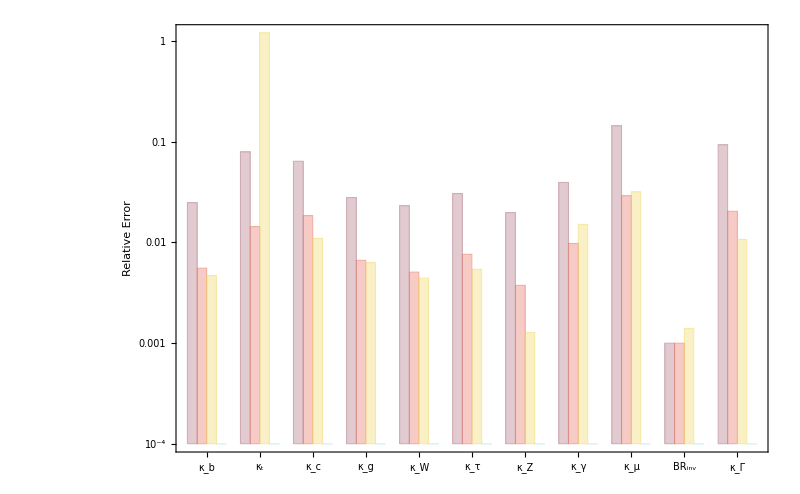

```mathematica
data1={MuC310pdata[[1]],MuC1010pdata[[1]],cepc36010pdata[[1]],MuC10cepc360LHC10pdata[[5]]};
plot=Table[Table[data1[[j,i]],{i,1,Length[data1[[1]]],1}],{j,1,Length[data1],1}];
p10fit1=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubscriptBox[\(BR\), \(inv\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,10},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{ColorData[24][8],ColorData[24][1],ColorData[24][3],ColorData[24][4]}},BaseStyle->28,PlotRange->{{1,61},{1*10^-4,1.2}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

### MuC10TeV+HLLHC, CEPC240GeV+HLLHC, CEPC240+360GeV+HLLHC, MuC10TeV+CEPC240+360GeV+HLLHC+MuC125GeV

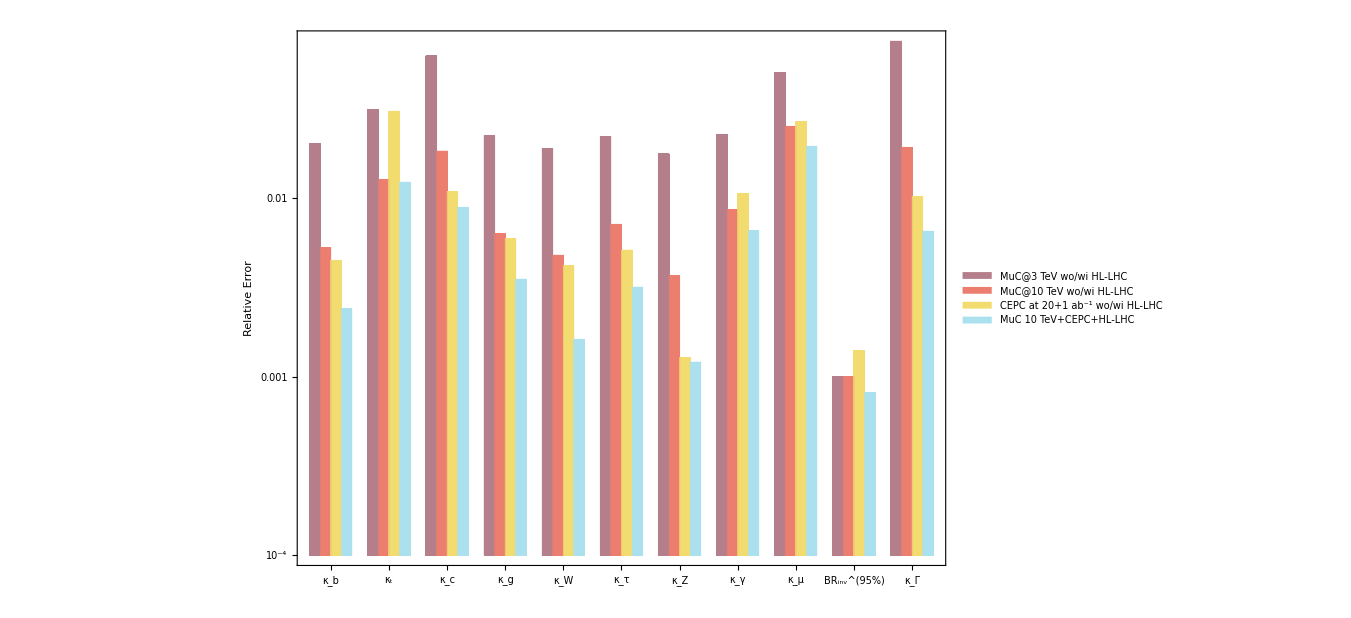

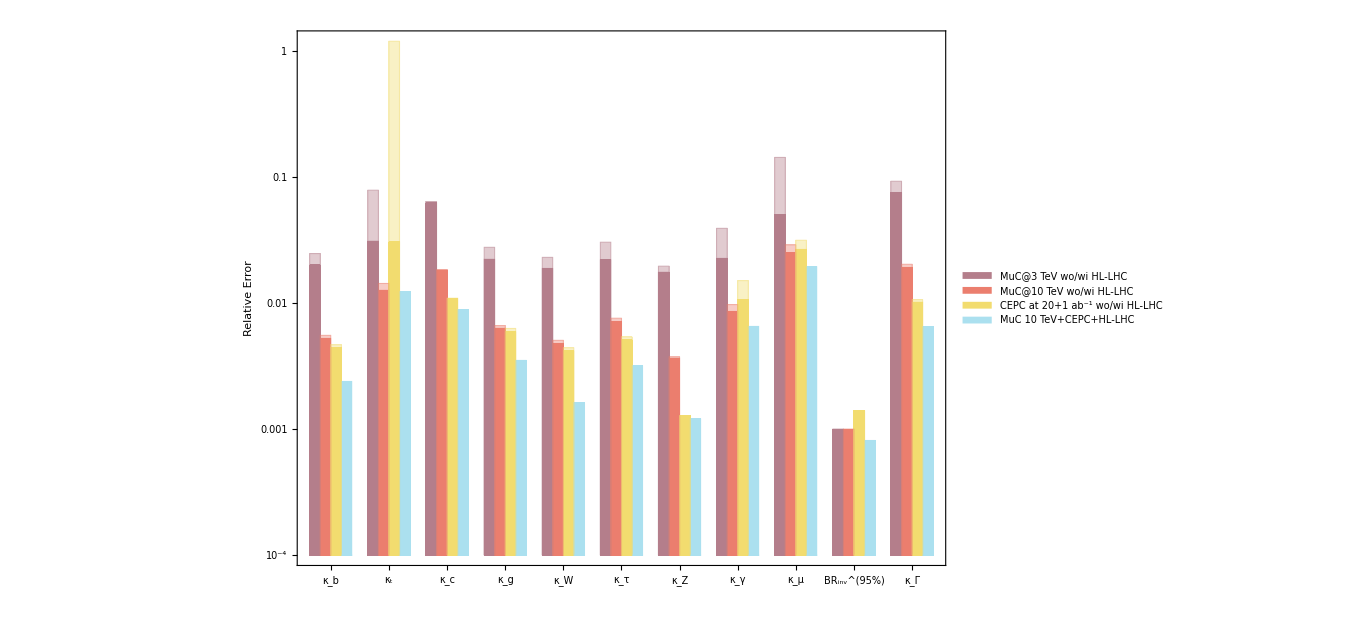

```mathematica
data2={MuC310pdata[[2]],MuC1010pdata[[2]],cepc36010pdata[[2]],MuC10cepc360LHC10pdata[[2]]};
plot=Table[Table[data2[[j,i]],{i,1,Length[data2[[1]]],1}],{j,1,Length[data2],1}];
p10fit2=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (11-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,10},{j,-4,1}],1]},ChartStyle->{ColorData[24][8],ColorData[24][1],ColorData[24][3],ColorData[24][4]},BaseStyle->28,PlotRange->{{1,62},{1*10^-4,1.2}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->1000,ChartLegends->Placed[{Style["MuC@3 TeV wo/wi HL-LHC",18],Style["MuC@10 TeV wo/wi HL-LHC",18],Style["CEPC at 20+1 ab^-1 wo/wi HL-LHC",18],Style["MuC 10 TeV+CEPC+HL-LHC",18]},Scaled[{{0.22,0.64},{0,0}}]]]
Show[p10fit2,p10fit1]
```

### only MuC 3TeV, only MuC 10TeV, only CEPC 240GeV

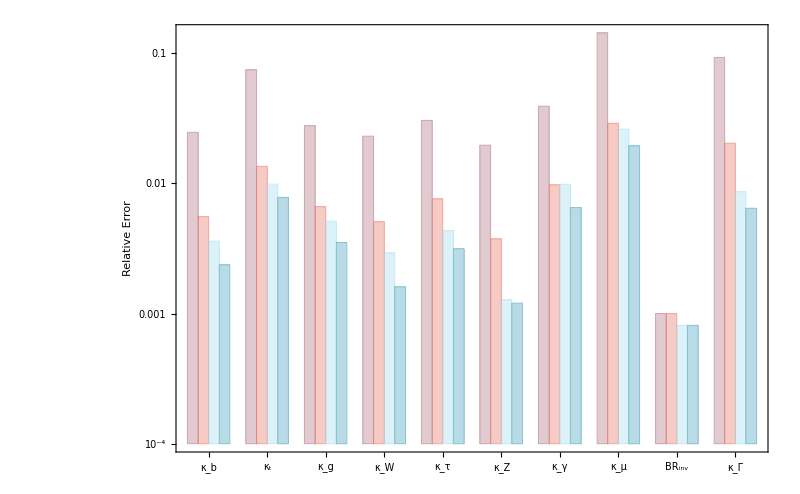

```mathematica
data1={MuC3MuC12510pdata[[1]],MuC10MuC12510pdata[[1]],MuC10cepc360LHC10pdata[[1]],MuC10cepc360LHC10pdata[[2]]};
plot=Table[Table[data1[[j,i]],{i,1,Length[data1[[1]]],1}],{j,1,Length[data1],1}];
p10fit1=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubsuperscriptBox[\(BR\), \(inv\), \(95%\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,11},{j,-4,1}],1]},ChartStyle->{{Directive[EdgeForm[Dashed],Opacity[0.4]]},{ColorData[24][8],ColorData[24][1],ColorData[24][4],ColorData[24][5]}},BaseStyle->28,PlotRange->{{1,55},{1*10^-4,0.5}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800]
```

### MuC3TeV+125GeV, MuC10TeV+125GeV, CEPC240GeV+360GeV

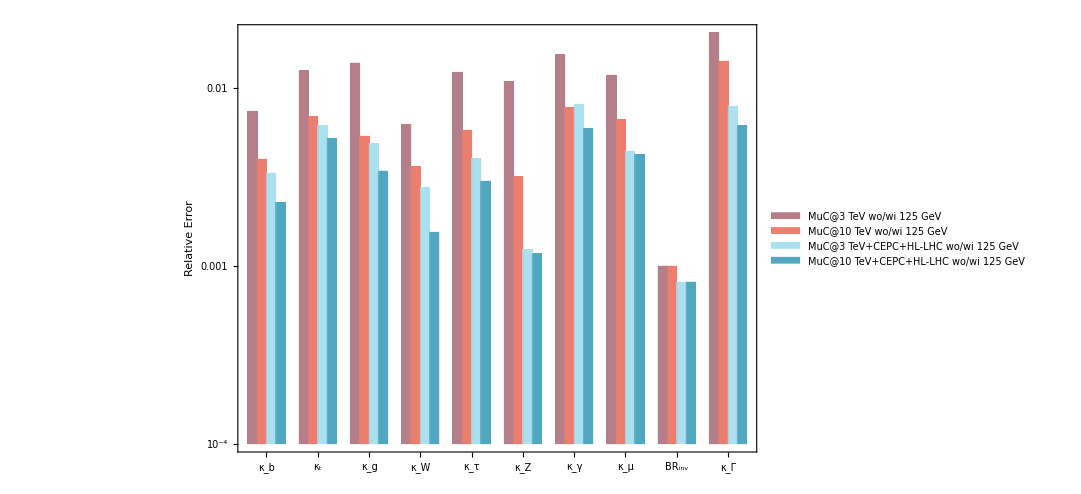

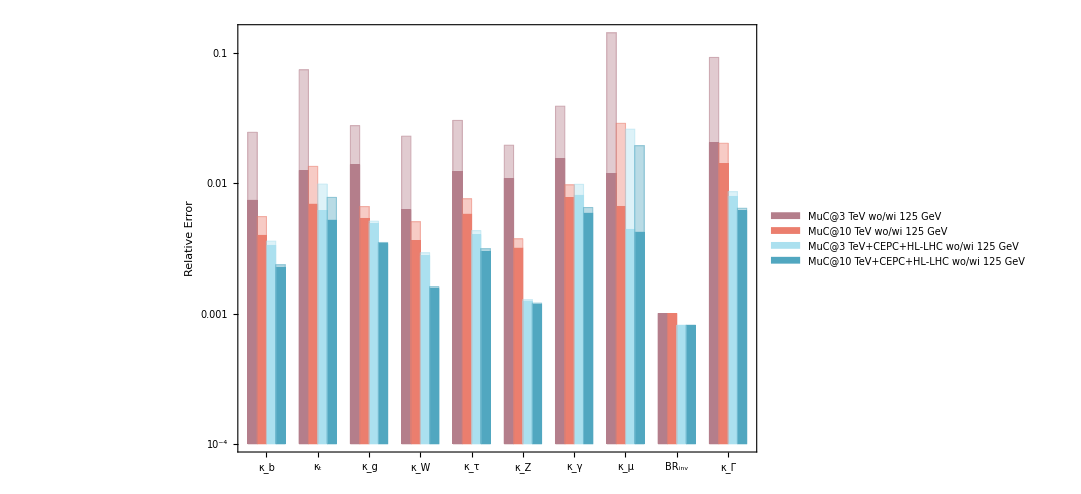

```mathematica
data2={MuC3MuC12510pdata[[2]],MuC10MuC12510pdata[[2]],MuC10cepc360LHC10pdata[[3]],MuC10cepc360LHC10pdata[[4]]};
plot=Table[Table[data2[[j,i]],{i,1,Length[data2[[1]]],1}],{j,1,Length[data2],1}];
p10fit2=BarChart[%ᵀ,ScalingFunctions->"Log",Frame->True,ChartLabels->{{"κ_b","κ_t","κ_c","κ_g","κ_W","κ_τ","κ_Z","κ_γ","κ_μ",Style["\!\(\*SubscriptBox[\(BR\), \(inv\)]\)",25],"κ_Γ"},None},FrameLabel->{{"Relative Error",None},{None,Style["Precision of Higgs coupling measurement (10-parameter Fit)",23]}},FrameStyle->Thick,GridLines->{None,Flatten[Table[{i*10^j,If[i==1,Directive[Black],Directive[Gray,Dashed]]},{i,1,11},{j,-4,1}],1]},ChartStyle->{ColorData[24][8],ColorData[24][1],ColorData[24][4],ColorData[24][5]},BaseStyle->28,PlotRange->{{1,55},{1*10^-4,1}},BarSpacing->{0,1.5},FrameTicks->{{{{0.001,"10^-3"},{0.01,"10^-2"},{0.1,"10^-1"},1},Automatic},{Automatic,None}},PlotRangePadding->0,ImageSize->800,ChartLegends->Placed[{Style["MuC@3 TeV wo/wi 125 GeV",18],Style["MuC@10 TeV wo/wi 125 GeV",18],Style["MuC@3 TeV+CEPC+HL-LHC wo/wi 125 GeV",18],Style["MuC@10 TeV+CEPC+HL-LHC wo/wi 125 GeV",18]},Scaled[{{0.14,0.55},{0,0}}]]]
Show[p10fit2,p10fit1]
```